## Lyapunov function to stabilize pendulum “up” solution Problem 11.17

```mathematica
Clear["Global`*"];
```

NDSolveValue::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

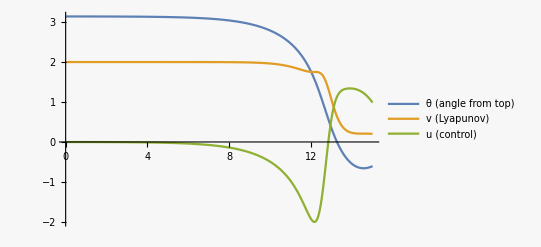

```mathematica
tend=15;
{θsol,vsol,usol}=NDSolveValue[{θ''[t]-Sin[θ[t]]==u[t],
u[t]==-(a+1) Sin[θ[t]]-θ'[t] Cos[θ[t]]^2-ϵ Mod[θ[t],2π,-π],
 v[t]==2a Sin[θ[t]/2]^2+1/2(θ'[t])^2,
θ[0]==π-0.001,θ'[0]==0}/.{a->1,ϵ->0.0},{θ,v,u},{t,0,tend}];
Plot[{θsol[t],vsol[t],usol[t]},{t,0,tend},PlotRange->All,PlotLegends->LineLegend[{"θ (angle from top)","v (Lyapunov)","u (control)"},LegendFunction->Frame]]
```

Export data

```mathematica
dt=0.01;
θt=Table[θsol[t],{t,0,tend,dt}];
vt=Table[vsol[t],{t,0,tend,dt}];
ut=Table[usol[t],{t,0,tend,dt}];
(* 
SetDirectory[NotebookDirectory[]];
Export["pendulumStabilization.dat",Flatten/@Transpose[{θt,vt,ut}],"Table"];
*)
```

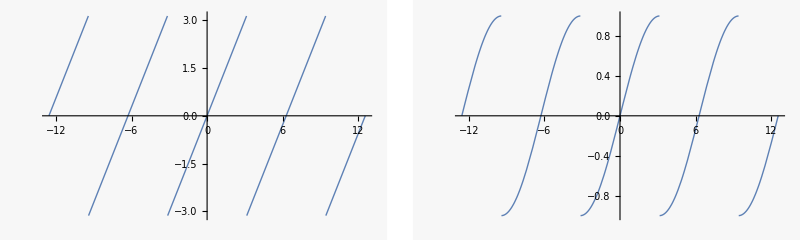

```mathematica
GraphicsRow[{Plot[Mod[x,2π,-π],{x,-4π,4π}],Plot[Sin[Mod[x,2π,-π]/2],{x,-4π,4π}]}]
```